```mathematica
ClearAll["Global`*"]
```

```mathematica
tag ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
```

```mathematica
L=4;
For[n=1,n≤4,n++,
For[i=1,i≤L,i++,
F =Import["/Users/danielgladstone/Documents/twitter_project/auto_graphing/"<>tag[[n]]<>"1039"<>"/"<>DateString[{2013,4,15,(5+i),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}]];
GList[tag[[n]]][i]=DeleteDuplicates[Table[
joined=First[F[[j]]]->Last[F[[j]]]
,{j,1,Length[F]}]];
G[tag[[n]]][i]=Graph[GList[tag[[n]]][i]];
G[VC][tag[[n]]][i]=VertexCount[G[tag[[n]]][i]];
G[VID][tag[[n]]][i]=Mean[VertexInDegree[G[tag[[n]]][i]]];
G[CC][tag[[n]]][i]=Mean[ClosenessCentrality[G[tag[[n]]][i]]];
G[GD][tag[[n]]][i]=GraphDensity[G[tag[[n]]][i]];
G[GR][tag[[n]]][i]=GraphReciprocity[G[tag[[n]]][i]];
G[GCC][tag[[n]]][i]=GlobalClusteringCoefficient[G[tag[[n]]][i]];
G[GA][tag[[n]]][i]=GraphAssortativity[G[tag[[n]]][i]];
G[MND][tag[[n]]][i]=Mean[MeanNeighborDegree[G[tag[[n]]][i]]];
G[MDC][tag[[n]]][i]=Mean[MeanDegreeConnectivity[G[tag[[n]]][i]]];
]]
```

```mathematica
G[VC]["#prayforboston"][96]
```

7

VC

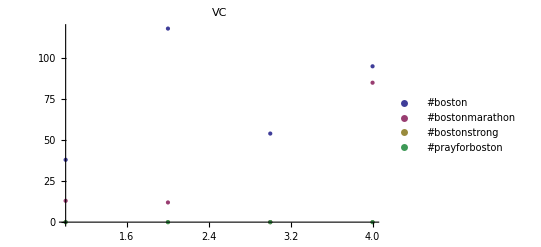
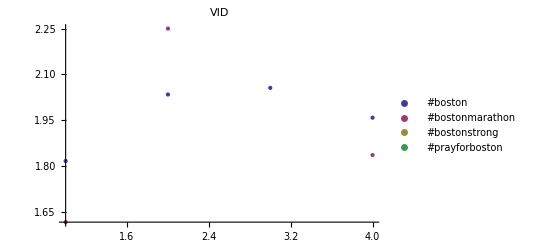
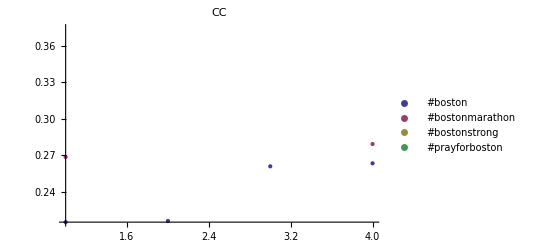
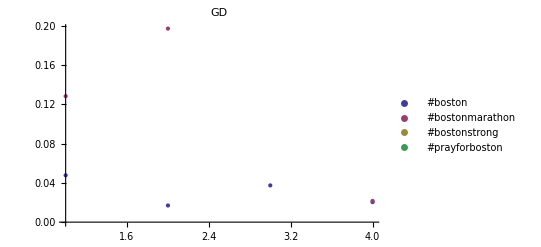
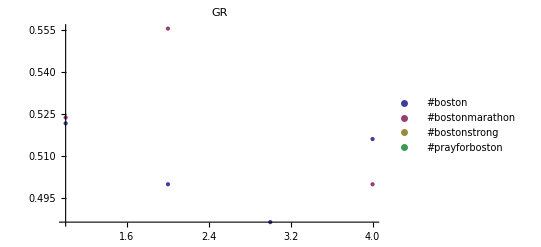
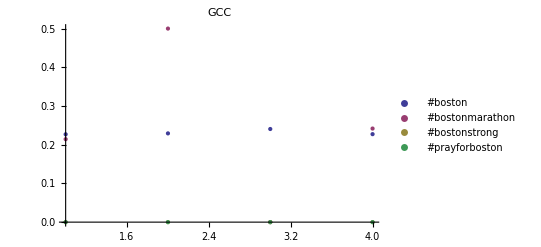
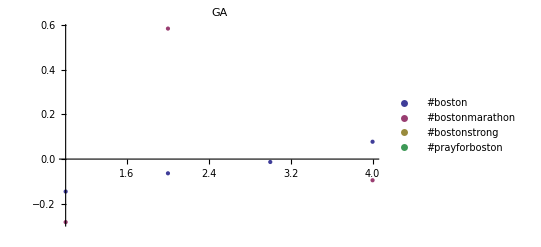
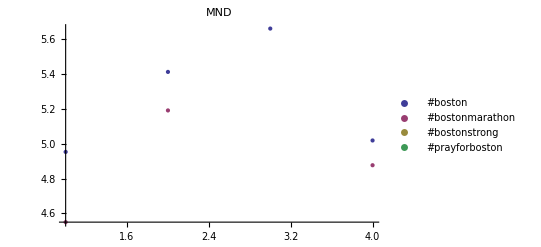

```mathematica
type={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
type[[1]]
For[p=1,p≤9,p++,
GType=type[[p]];
data=Table[
Table[
G[GType][tag[[n]]][i],{i,L}]
,{n,1,4}(*slect what hashtags to see here i.e.#prayforboston is (n,4,4)*)
];
d[type[[p]]]=data;
]

Table[ListPlot[d[type[[o]]],PlotLabel->type[[o]], PlotLegends->Table[
tag[[t]],{t,1,4}]],{o,9}]
```

```mathematica
Range[Length[namelist]]
Table[VC[j],{j,Length[namelist]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

{4,13,105,57,95,67,64,68,0,8,79,0}

```mathematica
G=Graph[GList]

VertexCount[G]
Mean[VertexInDegree[G]]
Mean[ClosenessCentrality[G]]
GraphDensity[G]
GraphReciprocity[G]
GlobalClusteringCoefficient[G]
GraphAssortativity[G]
Mean[MeanNeighborDegree[G]]
Mean[MeanDegreeConnectivity[G]]
```

-Graphics-

4

2

0.9375

2/3

3/4

3/5

0

9/2

7/3

```mathematica
First[F[[1]]]->Last[F[[1]]]
```

#cat→#cats

```mathematica
.
```

```mathematica
Table[
Print[i];
,{i,2,5}]
```

2

3

4

5

{Null,Null,Null,Null}